```mathematica
i=Sqrt[-1];
m={{0,1,0,-b*Exp[i*k*a]},
	{1,0,b*Exp[-i*k*a],0},
	{0,b*Exp[i*k*a],0,-1},
	{-b*Exp[-i*k*a],0,-1,0}}
```

```mathematica
{{0,1,0,-b ⅇ^(ⅈ a k)},{1,0,b ⅇ^(-ⅈ a k),0},{0,b ⅇ^(ⅈ a k),0,-1},{-b ⅇ^(-ⅈ a k),0,-1,0}}
```

```mathematica
Eigenvalues[m,Quartics->True]
```

{-ⅇ^(-1/2 ⅈ a k) √(b+ⅇ^(ⅈ a k)+b^2 ⅇ^(ⅈ a k)+b ⅇ^(2 ⅈ a k)),ⅇ^(-1/2 ⅈ a k) √(b+ⅇ^(ⅈ a k)+b^2 ⅇ^(ⅈ a k)+b ⅇ^(2 ⅈ a k)),-ⅇ^(-ⅈ a k) √(-b ⅇ^(ⅈ a k)+ⅇ^(2 ⅈ a k)+b^2 ⅇ^(2 ⅈ a k)-b ⅇ^(3 ⅈ a k)),ⅇ^(-ⅈ a k) √(-b ⅇ^(ⅈ a k)+ⅇ^(2 ⅈ a k)+b^2 ⅇ^(2 ⅈ a k)-b ⅇ^(3 ⅈ a k))}

```mathematica
e1[b_,k_]:=Sqrt[b^2+1+2*b*Cos[k]];
e2[k_]:=Sqrt[b^2+1-2*b*Cos[k]];
```

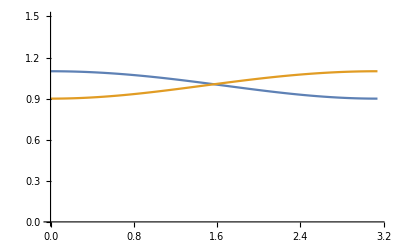

```mathematica
Plot[{e1[k],e2[k]},{k,0,Pi},PlotRange->{{0,Pi},{0,1.5}}]
```

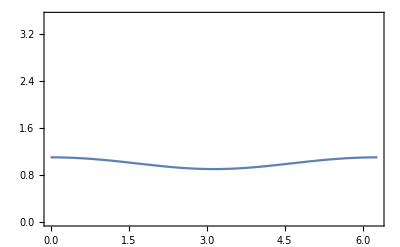

```mathematica
Plot[{e1[k]},{k,0,2*Pi},PlotRange->{{0,2*Pi},{0,3.5}},Frame -> True]
```

```mathematica
Manipulate[Plot[{e1[b,k]},{k,0,2*Pi},PlotRange->{{0,2*Pi},{0,3.5}},Frame -> True],{b,0,4.,0.1}]
```